```mathematica
Expand[Assuming[r>0,Solve[3r^2-3*(r^2+4α)*f[r]+6*α*f[r]^2==c,f[r]]]]
```

{{f[r]→1+r^2/(4 α)-(√(3 r^4+8 c α+48 α^2))/(4 √3 α)},{f[r]→1+r^2/(4 α)+(√(3 r^4+8 c α+48 α^2))/(4 √3 α)}}

## Tendencia Gauss Bonnet

```mathematica
Clear[ff1,ff2,α,μ,c]
```

En Gauss Bonnet existen dos soluciones de f(r), una positiva y otra negativa

```mathematica
ff1:=Assuming[r>0,Simplify[1+r^2/(4 α)+1/4 √(1/α) √(r^4/α+16 α (1+c))]]
```

```mathematica
ff2:=Assuming[r>0,Simplify[1+r^2/(4 α)-1/4 √(1/α) √(r^4/α+16 α (1+c))]]
```

Para el Apendice, agregar esta solución no física (α>0) que si es física para α<0 con α=-l^2/4

```mathematica
ff3=1-r^2/(l^2)+Sqrt[(r^4)/(l^4)+(1-c)]
```

1-r^2/l^2+√(1-c+r^4/l^4)

```mathematica
Assuming[r>0&&l>0,Series[ff3,{r,Infinity,2}]]
```

1-((-1+c) l^2)/(2 r^2)+O[1/r]^3

```mathematica
Solve[ff3==0,r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(√c l)/(√2)},{r→(√c l)/(√2)}}

### Tendencia para r->Infinito

Solución no física

```mathematica
Assuming[r>0&&α>0,Simplify[Series[Simplify[ff1],{r,Infinity,2}]]]
```

r^2/(2 α)+1+(2 (1+c) α)/r^2+O[1/r]^3

```mathematica
PowerExpand[Series[Simplify[Assuming[l>0,ff1/.α->-(l^2)/2]],{r,Infinity,2}]]
```

-r^2/l^2+1-((1+c) l^2)/r^2+O[1/r]^3

Como se puede observar, todos los términos suman a la unidad y por lo tanto no puede haber un horizonte de eventos. Esta es una solución no-física y crece de manera cuadrática en el infinito de manera muy similar como se comporta  el espacio-tiempo con constante cosmológica. (1/2α = -1/l^2) No tiene sentido físico, tiene 0 pero asíntoticamente no es deSitter

Solución física

```mathematica
Assuming[r>0&&α>0,Simplify[Series[Simplify[ff2],{r,Infinity,2}]]]
```

1-(2 ((1+c) α))/r^2+O[1/r]^3

Se puede apreciar que en la solución 2 tiende a 1 cuando r se aproxima a infinito. Además el término cuadrático está relacionado al término de masa.

```mathematica
Solve[2 α (1+c)==μ,c]
```

{{c→(-2 α+μ)/(2 α)}}

```mathematica
c:=Simplify[(-2 α+μ)/(2 α)]
```

```mathematica
PowerExpand[ff2,Assumptions->{α>0,r>0}]
```

1+r^2/(4 α)-(√(r^4/α+8 μ))/(4 √α)

```mathematica
Assuming[r>0&&α>0,Simplify[Series[Simplify[ff2],{r,Infinity,2}]]]
```

1-μ/r^2+O[1/r]^3

```mathematica
ff4:=Assuming[r>0,Simplify[1+r^2-√(r^4+μ/2)]]
```

```mathematica
Solve[ff4==0,r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-1/2 √(-2+μ)},{r→(√(-2+μ))/2}}

### Tendencia para r-> 0

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[ff4],{r,0,2}]]]
```

(1-(√μ)/(√2))+r^2+O[r]^3

```mathematica
Assuming[r>0&&α>0&&μ>0,Simplify[Series[Simplify[ff2],{r,0,2}]]]
```

(1-μ/(√2 √(α μ)))+r^2/(4 α)+O[r]^3

### Isotermas para ff1 y ff2

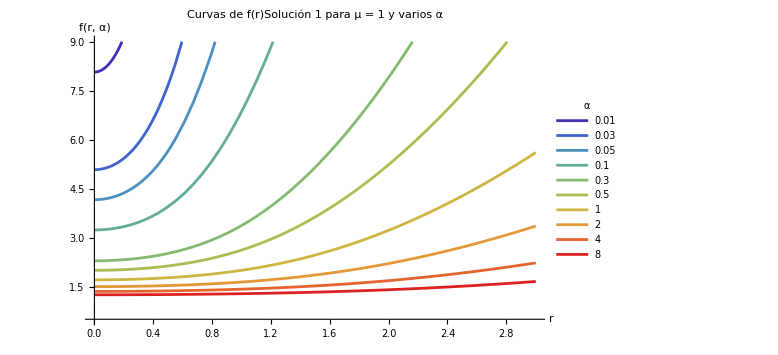

```mathematica
μ:=1;
valoresAlpha:={0.01,0.03,0.05,0.1,0.3,0.5,1,2,4,8};
Plot[Evaluate@Table[ff1,{α,valoresAlpha}],{r,0,3},PlotRange->{0.5,9},PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresAlpha]],{i,Length[valoresAlpha]}],PlotLegends->Placed[LineLegend[valoresAlpha,LegendLabel->Style["α",Bold]],{0.8,0.35}],AxesLabel->{"r","f(r, α)"},PlotLabel->Style["Curvas de f(r)Solución 1 para μ = 1 y varios α",14,Bold],ImageSize->Large]
```

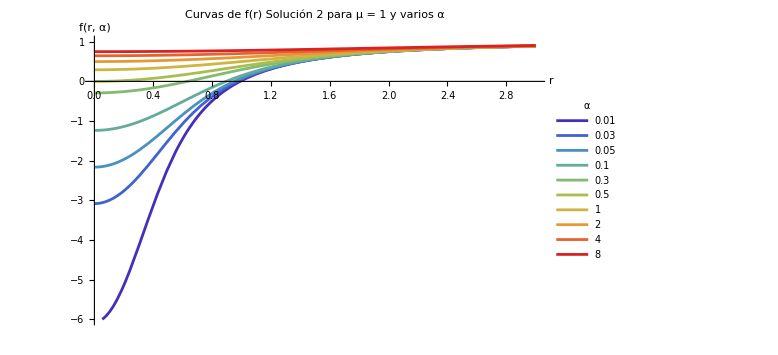

```mathematica
Plot[Evaluate@Table[ff2,{α,valoresAlpha}],{r,0,3},PlotRange->{-6,1},PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresAlpha]],{i,Length[valoresAlpha]}],PlotLegends->Placed[LineLegend[valoresAlpha,LegendLabel->Style["α",Bold]],{0.8,0.35}],AxesLabel->{"r","f(r, α)"},PlotLabel->Style["Curvas de f(r) Solución 2 para μ = 1 y varios α",14,Bold],ImageSize->Large]
```

### Isotermas para ff1 y ff2 variando μ

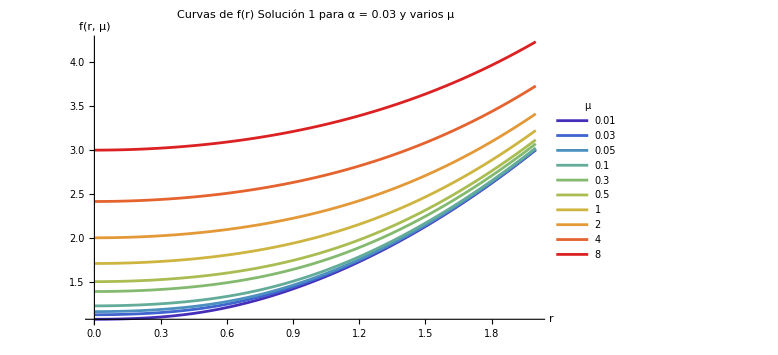

```mathematica
Clear[μ]
α:=1;
valoresMu:={0.01,0.03,0.05,0.1,0.3,0.5,1,2,4,8};
Plot[Evaluate@Table[ff1,{μ,valoresMu}],{r,0,2},PlotRange->Automatic,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ",Bold]],{0.8,0.35}],AxesLabel->{"r","f(r, μ)"},PlotLabel->Style["Curvas de f(r) Solución 1 para α = 0.03 y varios μ",14,Bold],ImageSize->Large]
```

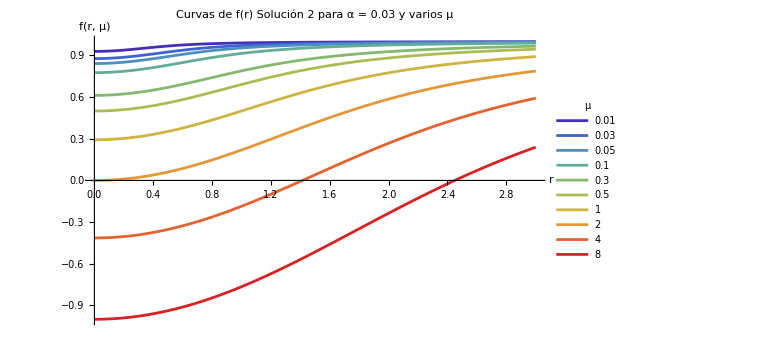

```mathematica
valoresMu:={0.01,0.03,0.05,0.1,0.3,0.5,1,2,4,8};
Plot[Evaluate@Table[ff2,{μ,valoresMu}],{r,0,3},PlotRange->Automatic,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ",Bold]],{0.8,0.35}],AxesLabel->{"r","f(r, μ)"},PlotLabel->Style["Curvas de f(r) Solución 2 para α = 0.03 y varios μ",14,Bold],ImageSize->Large]
```

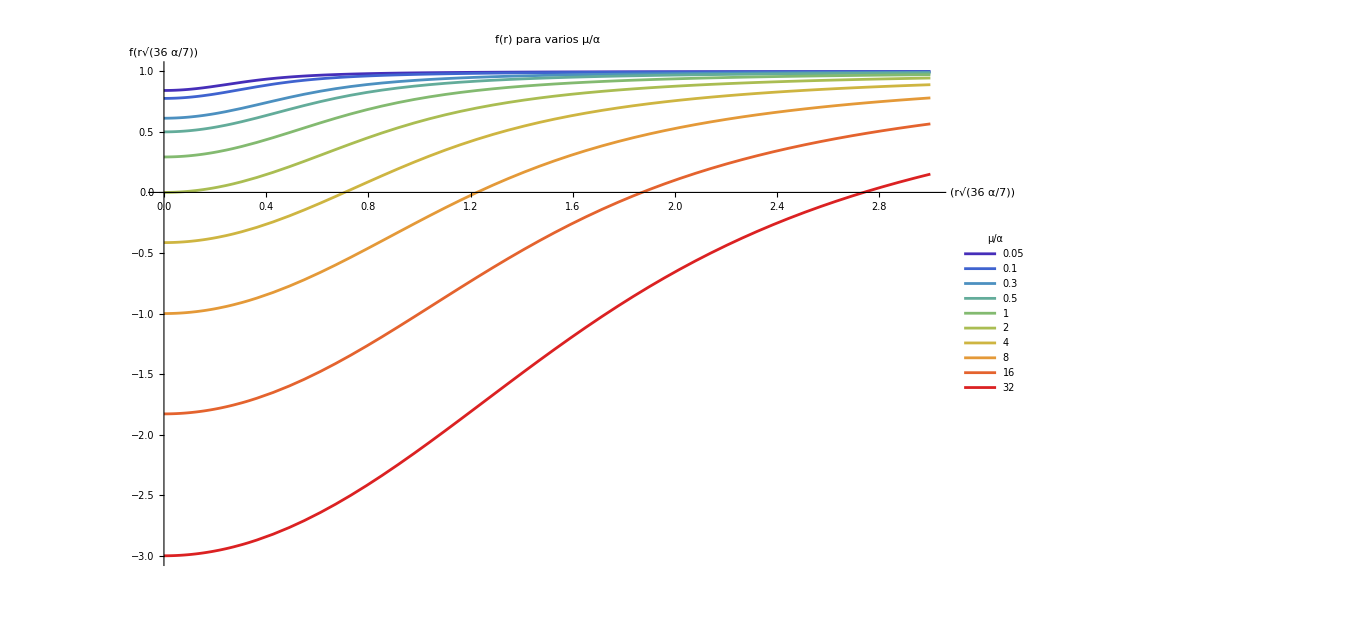

```mathematica
valoresMu:={0.05,0.1,0.3,0.5,1,2,4,8,16,32};fig1=Plot[Evaluate@Table[ff4,{μ,valoresMu}],{r,0,3},PlotRange->Automatic,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ/α",18,Bold]],{0.8,0.35}],AxesLabel->{Style["(r√(36  α/7))",18,Bold],Style["f(r√(36  α/7))",18,Bold]},PlotLabel->Style["f(r) para varios μ/α",20,Bold],ImageSize->{1000,600}]
```

```mathematica
Export["Gauss-Bonnet.png",fig1]
```

Gauss-Bonnet.png

### Invariante de Kretschmann

```mathematica
Clear[f,α,μ]
```

Para la solución 1

```mathematica
NN[r_]:=1
f[r_]:=ff1
Krt1[r_]=Assuming[r>0&&α>0,Simplify[1/(r^4 NN[r]^2)(9 r^4 f'[r]^2 NN'[r]^2+6 r^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+12 r^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r^2 f'[r] NN'[r]+r^4 f''[r] NN''[r])+4 f[r]^2 (3 r^2 NN'[r]^2+r^4 NN''[r]^2))]]
```

(3 (r^4+4 α μ+r^2 √(r^4+8 α μ)))/(2 r^4 α^2)

```mathematica
Series[Krt1[r],{r,Infinity,2}]
```

3/α^2+O[1/r]^3

```mathematica
Series[Krt1[r],{r,0,2}]
```

(6 μ)/(α r^4)+(3 √2 √(α μ))/(α^2 r^2)+3/(2 α^2)+(3 √(α μ) r^2)/(8 √2 α^3 μ)+O[r]^3

```mathematica
Plot3D[Krt1[r]/.μ->1,{α,0,2},{r,0,2},PlotRange->{0,100},AxesLabel->{"α","r","K1"},ColorFunction->"ThermometerColors",Mesh->None,PlotPoints->60]
```

-Graphics3D-

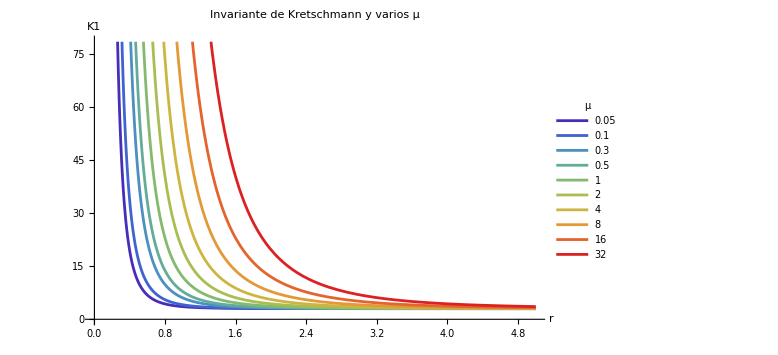

```mathematica
Plot[Evaluate@Table[Krt1[r]/.α->1,{μ,valoresMu}],{r,0,5},PlotRange->Automatic,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ",Bold]],{0.8,0.6}],AxesLabel->{"r","K1"},PlotLabel->Style["Invariante de Kretschmann y varios μ",14,Bold],ImageSize->Large]
```

Para la solución 2

```mathematica
Clear[NN,f]
NN[r_]:=1
f[r_]:=ff2
Krt2[r_]=Assuming[r>0&&α>0,Simplify[1/(r^4 NN[r]^2)(9 r^4 f'[r]^2 NN'[r]^2+6 r^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+12 r^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r^2 f'[r] NN'[r]+r^4 f''[r] NN''[r])+4 f[r]^2 (3 r^2 NN'[r]^2+r^4 NN''[r]^2))]]
```

(3 (r^4+4 α μ-r^2 √(r^4+8 α μ)))/(2 r^4 α^2)

```mathematica
Series[Krt2[r],{r,Infinity,2}]
```

O[1/r]^7

```mathematica
Series[Krt2[r],{r,0,2}]
```

(6 μ)/(α r^4)-(3 (√2 √(α μ)))/(α^2 r^2)+3/(2 α^2)-(3 √(α μ) r^2)/(8 (√2 α^3 μ))+O[r]^3

```mathematica
Plot3D[Krt2[r]/.μ->1,{α,0,1},{r,0,3},PlotRange->Automatic,AxesLabel->{"α","r","K2"},ColorFunction->"ThermometerColors",Mesh->None,PlotPoints->60]
```

-Graphics3D-

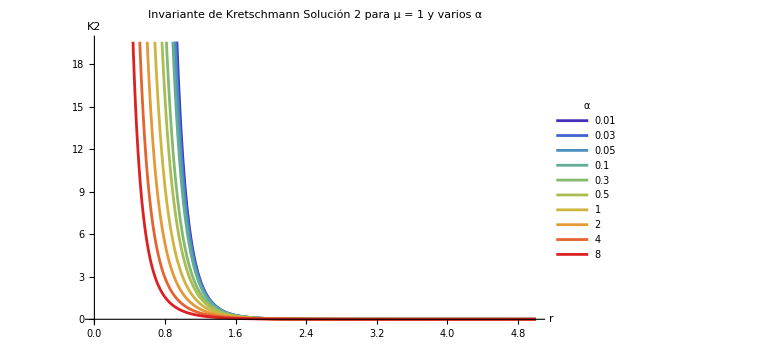

```mathematica
Plot[Evaluate@Table[Krt2[r]/.μ->1,{α,valoresAlpha}],{r,0,5},PlotRange->Automatic,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresAlpha]],{i,Length[valoresAlpha]}],PlotLegends->Placed[LineLegend[valoresAlpha,LegendLabel->Style["α",Bold]],{0.8,0.6}],AxesLabel->{"r","K2"},PlotLabel->Style["Invariante de Kretschmann Solución 2 para μ = 1 y varios α",14,Bold],ImageSize->Large]
```

Kretschman para la función escalada

```mathematica
Clear[NN,f]
NN[r_]:=1
f[r_]:=ff4
Krt4[r_]=Assuming[r>0,Simplify[1/(r^4 NN[r]^2)(9 r^4 f'[r]^2 NN'[r]^2+6 r^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+12 r^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r^2 f'[r] NN'[r]+r^4 f''[r] NN''[r])+4 f[r]^2 (3 r^2 NN'[r]^2+r^4 NN''[r]^2))]]
```

6 (4+μ/r^4-(2 √2 √(2 r^4+μ))/r^2)

```mathematica
Series[Krt4[r],{r,Infinity,8}]
```

(3 μ^2)/(4 r^8)+O[1/r]^9

```mathematica
Series[Krt4[r],{r,0,2}]
```

(6 μ)/r^4-(12 (√2 √μ))/r^2+24-(12 √2 r^2)/(√μ)+O[r]^3

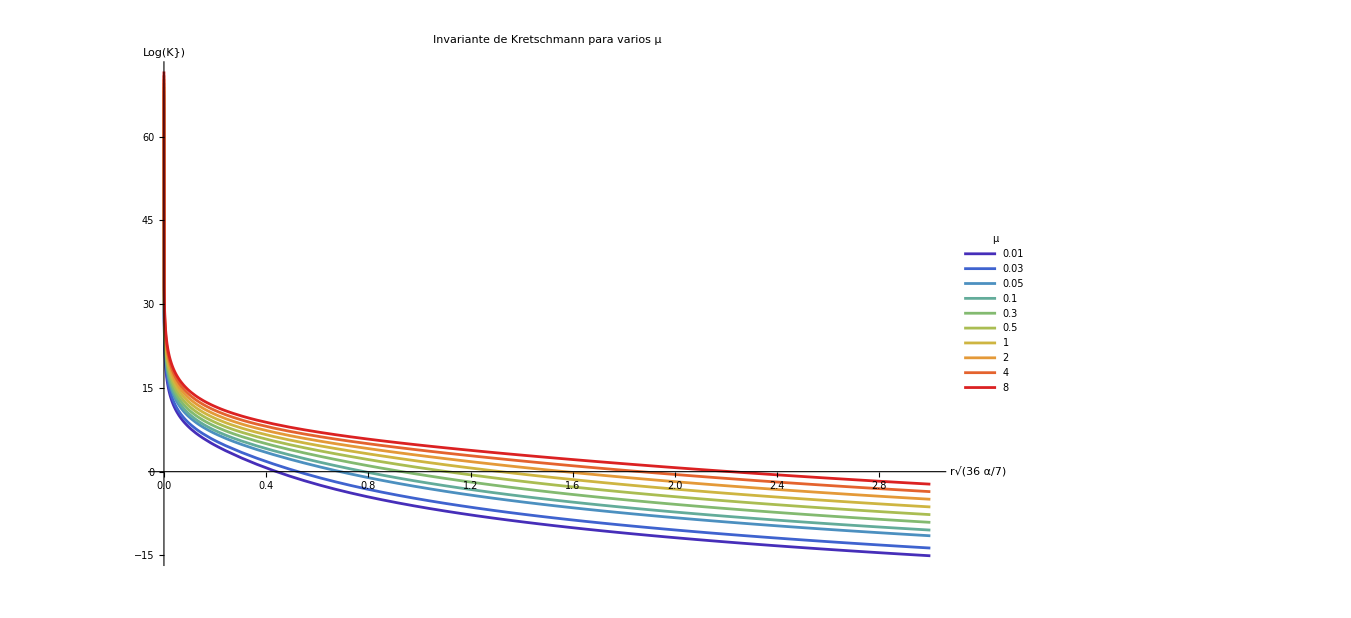

```mathematica
fig2=Plot[Evaluate@Table[Log[Krt4[r]],{μ,valoresMu}],{r,0,3},PlotRange->All,PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresAlpha]],{i,Length[valoresAlpha]}],PlotLegends->Placed[LineLegend[valoresAlpha,LegendLabel->Style["μ",16,Bold]],{0.8,0.7}],AxesLabel->{Style["r√(36  α/7)",15,Bold],Style["Log(K})",15,Bold]},PlotLabel->Style["Invariante de Kretschmann para varios μ",18,Bold],ImageSize->{1000,600}]
```

```mathematica
Export["Gauss-Bonnet Kretschmann.png",fig2]
```

Gauss-Bonnet Kretschmann.png

```mathematica
FullSimplify[6 (4+μ/r^4-(2 √2 √(2 r^4+μ))/r^2),Assumptions->r>0]
```

6 (4+μ/r^4-(2 √2 √(2 r^4+μ))/r^2)

```mathematica
Solve[Log[x]==24,x]
```

{{x→ⅇ^24}}

```mathematica
N[{{x->ⅇ^24}}]
```

{{x→2.64891×10^10}}